# Plots of Experiment Results

```mathematica
ClearAll
```

ClearAll

## Functions to Generate Pretty Plots

### 3D Plot

```mathematica
Clear[plotExperimentResults];
plotExperimentResults[alg_,initSolType_,k_,realizations_,seed_,currentDir_,nList_,mList_,scheduleToTest_]:=plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]=Module[
(* Put local variables here *)
{makespanGapDataPath,runtimeDataPath,makespanGapRawData,runtimeRawData,makespanGapData,runtimeData,index},

Clear[makespanGapDataPath,runtimeDataPath,makespanGapRawData,runtimeRawData,makespanGapData,runtimeData,index];

(* Define data to import *)
If [scheduleToTest== "Simple"||scheduleToTest== "LinMult"||scheduleToTest== "QuadMult"||scheduleToTest== "ExpMult",
If[seed==1,
makespanGapDataPath=currentDir<>ToString[StringForm["data/makespanGap_``_``_k``-``_seeded_``.csv",alg,initSolType,k,realizations,scheduleToTest]];
runtimeDataPath=currentDir<>ToString[StringForm["data/runtime_``_``_k``-``_seeded_``.csv",alg,initSolType,k,realizations,scheduleToTest]];,
makespanGapDataPath=currentDir<>ToString[StringForm["data/makespanGap_``_``_k``-``_noSeed_``.csv",alg,initSolType,k,realizations,scheduleToTest]];
runtimeDataPath=currentDir<>ToString[StringForm["data/runtime_``_``_k``-``_noSeed_``.csv",alg,initSolType,k,realizations,scheduleToTest]];
],
If[seed==1,
makespanGapDataPath=currentDir<>ToString[StringForm["data/makespanGap_``_``_k``-``_seeded.csv",alg,initSolType,k,realizations]];
runtimeDataPath=currentDir<>ToString[StringForm["data/runtime_``_``_k``-``_seeded.csv",alg,initSolType,k,realizations]];,
makespanGapDataPath=currentDir<>ToString[StringForm["data/makespanGap_``_``_k``-``_noSeed.csv",alg,initSolType,k,realizations]];
runtimeDataPath=currentDir<>ToString[StringForm["data/runtime_``_``_k``-``_noSeed.csv",alg,initSolType,k,realizations]];
]
];

(* Import the data *)
Print["Searching for data files at\n\t",makespanGapDataPath];
makespanGapRawData=Import[makespanGapDataPath];
runtimeRawData=Import[runtimeDataPath];

(* Initialize plot data *)
makespanGapData=ConstantArray[0,{(Length[nList])*Length[mList]}];
runtimeData=ConstantArray[0,{(Length[nList])*Length[mList]}];

(* Process data into an easily plottable form *)
For[i=1,i≤Length[mList],i++,
For[j=1,j≤Length[nList],j++,
index=(i-1)*Length[nList]+j;
makespanGapData⟦index⟧={mList⟦i⟧,nList⟦j⟧,makespanGapRawData⟦i,j⟧};
runtimeData⟦index⟧={mList⟦i⟧,nList⟦j⟧,runtimeRawData⟦i,j⟧};
];
];

(* Plot makespan gap as a percentage between 0 and 20 *)

ListPlot3D[makespanGapData,Mesh->All,AxesLabel->{"Machines","Jobs","Makespan Gap\n(percentage)"},ImageSize->400,PlotRange->{0,20},ColorFunction->"TemperatureMap",FaceGrids->{{0,0,-1},{1,0,0},{0,1,0}},ViewPoint->{-2,-1.99999,2}]

(* Plot runtime in between 0 and 1200 (20 mins) *)

ListPlot3D[runtimeData,Mesh->All,AxesLabel->{"Machines","Jobs","Run-time\n(seconds)"},ImageSize->400,PlotRange->{0,1200},ColorFunction->"TemperatureMap",FaceGrids->{{0,0,-1},{1,0,0},{0,1,0}},ViewPoint->{-2,-1.99999,2}]

];
```

### Loglog Plot

```mathematica
Clear[plotExperimentResultsLoglog];
plotExperimentResultsLoglog[alg_,initSolType_,k_,realizations_,seed_,currentDir_,nList_,mList_,dist_,plotColour_]:=plotExperimentResultsLoglog[alg,initSolType,k,realizations,seed,currentDir,nList,mList,dist,plotColour]=Module[
(* Put local variables here *)
{makespanGapDataPath,runtimeDataPath,makespanGapRawData,runtimeRawData,makespanGapData,runtimeData,index},

Clear[makespanGapRawData,runtimeRawData,makespanGapData,
runtimeData,index];

(* Define data to import *)
If[seed==1,
makespanGapDataPath=currentDir<>ToString[StringForm["data/makespanGap_``_``_k``-``_seeded_``.csv",alg,initSolType,k,realizations,dist]];
runtimeDataPath=currentDir<>ToString[StringForm["data/runtime_``_``_k``-``_seeded_``.csv",alg,initSolType,k,realizations,dist]];,
makespanGapDataPath=currentDir<>ToString[StringForm["data/makespanGap_``_``_k``-``_noSeed_``.csv",alg,initSolType,k,realizations,dist]];
runtimeDataPath=currentDir<>ToString[StringForm["data/runtime_``_``_k``-``_noSeed_``.csv",alg,initSolType,k,realizations,dist]];
];

(* Import the data *)
Print["Searching for data files at\n\t",runtimeDataPath];
makespanGapRawData=Import[makespanGapDataPath]⟦1⟧;
runtimeRawData=Import[runtimeDataPath]⟦1⟧;

(* Initialize plot data *)
makespanGapData=ConstantArray[0,Length[nList]];
runtimeData=ConstantArray[0,Length[nList]];

(* Process data into an easily plottable form *)
For[j=1,j≤Length[nList],j++,
makespanGapData⟦j⟧={nList⟦j⟧,makespanGapRawData⟦j⟧};
runtimeData⟦j⟧={nList⟦j⟧,runtimeRawData⟦j⟧};
];

(* Plot makespan gap as a percentage between 0 and 20 *)
ListLogLogPlot[makespanGapData,AxesLabel->{"Jobs","Makespan Gap\n(percentage)"},ImageSize->400,Ticks->Automatic,Joined->True,PlotMarkers->{●,10},PlotStyle->{plotColour},PlotLegends->{dist}]

(* Plot runtime in between 0 and 300 (5 mins) *)
ListLogLogPlot[runtimeData,AxesLabel->{"Jobs","Run-time\n(seconds)"},ImageSize->400,Ticks->Automatic,Joined->True,PlotMarkers->{●,10},PlotStyle->{plotColour},PlotLegends->{dist}]
];
```

## Question 1

### Part (c) Determining k

#### k=1

```mathematica
k=1;
alg="GLS";
initSolType="random";
realizations=20;
seed=0;
nList={15,20,25,30,35,40,45,50};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="NA";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_GLS_random_k1-20_noSeed.csv

-Graphics3D- -Graphics3D-

```mathematica
k=1;
alg="GLS";
initSolType="GMS";
realizations=1;
seed=0;
nList={15,20,25,30,35,40,45,50};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="NA";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_GLS_GMS_k1-1_noSeed.csv

#### k=2

```mathematica
k=2;
alg="GLS";
initSolType="random";
realizations=1;
seed=0;
nList={15,20,25,30,35,40,45,50};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="NA";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_GLS_random_k2-1_noSeed.csv

-Graphics3D- -Graphics3D-

```mathematica
k=2;
alg="GLS";
initSolType="GMS";
realizations=1;
seed=0;
nList={15,20,25,30,35,40,45,50};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="NA";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_GLS_GMS_k2-1_noSeed.csv

#### k=3

```mathematica
k=3;
alg="GLS";
initSolType="random";
realizations=1;
seed=0;
nList={15,20,25,30,35,40,45,50};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="NA";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_GLS_random_k3-1_noSeed.csv

-Graphics3D- -Graphics3D-

```mathematica
k=3;
alg="GLS";
initSolType="GMS";
realizations=1;
seed=0;
nList={10,20,30,40};
mList={2,3,4,5};
currentDir=NotebookDirectory[];
scheduleToTest="NA";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_GLS_GMS_k3-1_noSeed.csv

### Part (d) Testing the performance of GLS

Using a seed, we generate a set of input instances to the makespan scheduling problem. We run GLS on this set of instances using the k-value found in part (c) to determine the limits of our GLS algorithm. We decided a “reasonable” upper limit on the runtime of the algorithm was 5 minutes. Using both random and GMS initial solutions, we compare the results of these tests:

```mathematica
k=2;
alg="GLS";
initSolType="random";
realizations=10;
seed=1;
nList={10,20,30,40,50,60,70,80,90,100};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="NA";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_GLS_random_k2-10_seeded.csv

-Graphics3D- -Graphics3D-

```mathematica
k=2;
alg="GLS";
initSolType="GMS";
realizations=10;
seed=1;
nList={10,20,30,40,50,60,70,80,90,100};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="NA";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_GLS_GMS_k2-10_seeded.csv

-Graphics3D- -Graphics3D-

## Question 2

### Part (c) Testing the performance of VDS

```mathematica
k=2;
alg="VDS";
initSolType="random";
realizations=10;
seed=1;
nList={10,20,30,40,50,60,70,80,90,100};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="NA";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_VDS_random_k2-10_seeded.csv

-Graphics3D- -Graphics3D-

```mathematica
k=2;
alg="VDS";
initSolType="GMS";
realizations=10;
seed=1;
nList={10,20,30,40,50,60,70,80,90,100};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="NA";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_VDS_GMS_k2-10_seeded.csv

-Graphics3D- -Graphics3D-

## Question 3

### Testing simulated annealing with random and GMS initial solutions

```mathematica
k=2;
alg="Ours";
initSolType="random";
realizations=10;
seed=1;
nList={10,20,30,40,50,60,70,80,90,100};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="NA";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_Ours_random_k2-10_seeded.csv

-Graphics3D- -Graphics3D-

```mathematica
k=2;
alg="Ours";
initSolType="GMS";
realizations=10;
seed=1;
nList={10,20,30,40,50,60,70,80,90,100};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="NA";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_Ours_GMS_k2-10_seeded.csv

-Graphics3D- -Graphics3D-

### Testing simulated annealing with each of the 4 cooling schedules

```mathematica
k=2;
alg="Ours";
initSolType="random";
realizations=10;
seed=1;
nList={10,20,30,40,50,60,70,80,90,100};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="Simple";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_Ours_random_k2-10_seeded_Simple.csv

-Graphics3D- -Graphics3D-

```mathematica
k=2;
alg="Ours";
initSolType="random";
realizations=10;
seed=1;
nList={10,20,30,40,50,60,70,80,90,100};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="LinMult";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_Ours_random_k2-10_seeded_LinMult.csv

-Graphics3D- -Graphics3D-

```mathematica
k=2;
alg="Ours";
initSolType="random";
realizations=10;
seed=1;
nList={10,20,30,40,50,60,70,80,90,100};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="QuadMult";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_Ours_random_k2-10_seeded_QuadMult.csv

-Graphics3D- -Graphics3D-

```mathematica
k=2;
alg="Ours";
initSolType="random";
realizations=10;
seed=1;
nList={10,20,30,40,50,60,70,80,90,100};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="ExpMult";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_Ours_random_k2-10_seeded_ExpMult.csv

-Graphics3D- -Graphics3D-

### Testing the limits of Simulated Annealing

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/runtime_Ours_GMS_k2-10_seeded_uniform.csv

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/runtime_Ours_GMS_k2-10_seeded_fatTailed.csv

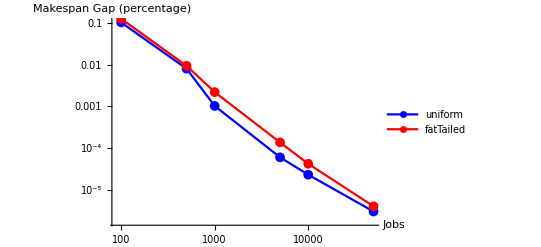

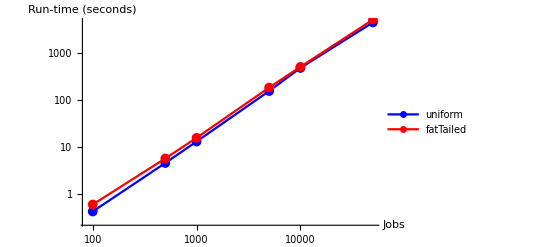

```mathematica
k=2;
alg="Ours";
initSolType="GMS";
realizations=10;
seed=1;
nList={100,500,1000,5000,10000,50000};
mList={2};
currentDir=NotebookDirectory[];

dist="uniform";
plotsUniform=plotExperimentResultsLoglog[alg,initSolType,k,realizations,seed,currentDir,nList,mList,dist,Blue];

dist="fatTailed";
plotsFatTailed=plotExperimentResultsLoglog[alg,initSolType,k,realizations,seed,currentDir,nList,mList,dist,Red];

(* Plot results on the same axis to compare the results *)
Show[plotsUniform⟦1⟧,plotsFatTailed⟦1⟧] 
Show[plotsUniform⟦2⟧,plotsFatTailed⟦2⟧]
```

### Comparing Simulated Annealing to GLS and VDS on the seeded instances

```mathematica
k=2;
alg="Ours";
initSolType="GMS";
realizations=10;
seed=1;
nList={10,20,30,40,50,60,70,80,90,100};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="NA";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_Ours_GMS_k2-10_seeded.csv

-Graphics3D- -Graphics3D-

### Testing pathological input instances for uniform and badly distributed processing times

```mathematica
plotPoints={{90,100},{450,500},{900,1000},{2700,3000},{4500,5000}};
currentDir=NotebookDirectory[];
dist="uniform";
makespanGapRawData=Import[currentDir<>ToString[StringForm["data/makespanGap_Ours_GMS_patho_``.csv",dist]]]⟦1⟧;
runtimeRawData=Import[currentDir<>ToString[StringForm["data/runtime_Ours_GMS_patho_``.csv",dist]]]⟦1⟧;

makespanGapDataUnif=ConstantArray[0,Length[plotPoints]];
runtimeDataUnif=ConstantArray[0,Length[plotPoints]];
For[j=1,j≤Length[plotPoints],j++,
makespanGapDataUnif⟦j⟧=Join[plotPoints⟦j⟧,{makespanGapRawData⟦j⟧}];
runtimeDataUnif⟦j⟧=Join[plotPoints⟦j⟧,{runtimeRawData⟦j⟧}];
];

dist="fatTailed";
makespanGapRawData=Import[currentDir<>ToString[StringForm["data/makespanGap_Ours_GMS_patho_``.csv",dist]]]⟦1⟧;
runtimeRawData=Import[currentDir<>ToString[StringForm["data/runtime_Ours_GMS_patho_``.csv",dist]]]⟦1⟧;

makespanGapDataBadDist=ConstantArray[0,Length[plotPoints]];
runtimeDataBadDist=ConstantArray[0,Length[plotPoints]];
For[j=1,j≤Length[plotPoints],j++,
makespanGapDataBadDist⟦j⟧=Join[plotPoints⟦j⟧,{makespanGapRawData⟦j⟧}];
runtimeDataBadDist⟦j⟧=Join[plotPoints⟦j⟧,{runtimeRawData⟦j⟧}];
];

Graphics3D[{Thick,Line[makespanGapDataUnif,VertexColors->{Blue,Blue,Blue,Blue,Blue}],Line[makespanGapDataBadDist,VertexColors->{Red,Red,Red,Red,Red}],PointSize[Large],Blue,Point[makespanGapDataUnif],Red,Point[makespanGapDataBadDist]},Axes->True,PlotRange->{0,200},ImageSize->500,AxesLabel->{"Machines","Jobs","Makespan Gap\n(percentage)"},FaceGrids->{{0,0,-1},{-1,0,0},{0,1,0}},ViewPoint->{1,-1.999,0.5}]

Graphics3D[{Thick,Line[runtimeDataUnif,VertexColors->{Blue,Blue,Blue,Blue,Blue}],Line[runtimeDataBadDist,VertexColors->{Red,Red,Red,Red,Red}],PointSize[Large],Blue,Point[runtimeDataUnif],Red,Point[runtimeDataBadDist]},Axes->True,PlotRange->{0,1000},ImageSize->500,AxesLabel->{"Machines","Jobs","Runtime\n(seconds)"},FaceGrids->{{0,0,-1},{-1,0,0},{0,1,0}},ViewPoint->{1,-1.999,0.5}]
```

-Graphics3D-

-Graphics3D-

```mathematica
DynamicModule[{v={1,-1.999,0.5}},Graphics3D[{Thick,Line[makespanGapDataUnif,VertexColors->{Blue,Blue,Blue,Blue,Blue}],Line[makespanGapDataBadDist,VertexColors->{Red,Red,Red,Red,Red}],PointSize[Large],Blue,Point[makespanGapDataUnif],Red,Point[makespanGapDataBadDist]},Axes->True,PlotRange->{0,1000},ImageSize->500,AxesLabel->{"Machines","Jobs","Makespan Gap\n(percentage)"},FaceGrids->Dynamic[Sign/@DiagonalMatrix[-v]],ViewPoint->Dynamic[v]]]

DynamicModule[{v={1,-1.999,0.5}},Graphics3D[{Thick,Line[runtimeDataUnif,VertexColors->{Blue,Blue,Blue,Blue,Blue}],Line[runtimeDataBadDist,VertexColors->{Red,Red,Red,Red,Red}],PointSize[Large],Blue,Point[runtimeDataUnif],Red,Point[runtimeDataBadDist]},Axes->True,PlotRange->{0,1000},ImageSize->500,AxesLabel->{"Machines","Jobs","Runtime\n(seconds)"},FaceGrids->Dynamic[Sign/@DiagonalMatrix[-v]],ViewPoint->Dynamic[v]]]
```

### Misc. Heuristic Plots

#### k=2: Compare random and GMS

```mathematica
k=2;
alg="Ours";
initSolType="random";
realizations=20;
seed=0;
nList={15,20,25,30,35,40,45,50};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList]
```

Searching for data files at
	/Users/pamelajenkins/Documents/Lotte/Approximation Algorithms/AAH-makespanScheduling-master/data/makespanGap_Ours_random_k2-20_noSeed.csv

-Graphics3D- -Graphics3D-

```mathematica
k=2;
alg="Ours";
initSolType="GMS";
realizations=20;
seed=0;
nList={15,20,25,30,35,40,45,50};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList]
```

Searching for data files at
	/Users/pamelajenkins/Documents/Lotte/Approximation Algorithms/AAH-makespanScheduling-master/data/makespanGap_Ours_GMS_k2-20_noSeed.csv

-Graphics3D- -Graphics3D-

#### k=3: Compare random and GMS

```mathematica
k=3;
alg="Ours";
initSolType="random";
realizations=20;
seed=0;
nList={15,20,25,30,35,40,45,50};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList]
```

Searching for data files at
	/Users/pamelajenkins/Documents/Lotte/Approximation Algorithms/AAH-makespanScheduling-master/data/makespanGap_Ours_random_k3-20_noSeed.csv

-Graphics3D- -Graphics3D-

```mathematica
k=3;
alg="Ours";
initSolType="GMS";
realizations=20;
seed=0;
nList={15,20,25,30,35,40,45,50};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList]
```

Searching for data files at
	/Users/pamelajenkins/Documents/Lotte/Approximation Algorithms/AAH-makespanScheduling-master/data/makespanGap_Ours_GMS_k3-20_noSeed.csv

-Graphics3D- -Graphics3D-

#### k=2: Testing parameter values

```mathematica
k=2;
alg="Ours";
initSolType="GMS";
realizations=2;
seed=0;
nList={15,20,25,30,35,40,45,50};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList]
```

Searching for data files at
	/Users/pamelajenkins/Documents/Lotte/Approximation Algorithms/AAH-makespanScheduling-master/data/makespanGap_Ours_GMS_k2-2_noSeed.csv

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics3D- -Graphics3D-

## Misc.

```mathematica
makespanGap_GLS_GMS_k2-10_seeded.csv
```

```mathematica
data=Import[NotebookDirectory[]<>ToString["data/makespanGap_GLS_random_k2-10_seeded.csv"]];
data2 =Flatten[data];
Total[Flatten[data]]/50
```

4.08852

```mathematica
data2={0.562121,0.059156,0.045784,0.00471,0.018915,0.020481,0.017549,0.010414,0.015479,0.01199,6.234147,0.544602,0.216755,0.100178,0.098224,0.051132,0.02417,0.043975,0.024559,0.022013,1.050728,0.363922,0.290944,0.147438,0.152703,0.06596,0.087081,0.096981,0.069544,5.636481,1.120444,0.502473,0.270786,0.373058,0.167367,0.116981,0.143705,0.152853,9.856704,2.125645,0.870795,0.641418,0.327437,0.264061,0.323505,0.27448,0.204319};
Total[data2]/47
```

0.719663

```mathematica
data=Import[NotebookDirectory[]<>ToString["data/makespanGap_GLS_GMS_k2-10_seeded.csv"]]
data2 =Flatten[data];
Total[Flatten[data]]/50
```

{{0.515456,0.05974,0.045784,0.00471,0.018915,0.020481,0.017549,0.010414,0.015479,0.01199},{6.4398,0.350746,0.161783,0.080704,0.067957,0.026905,0.02417,0.043975,0.024559,0.022013},{17.5153,1.53958,0.571611,0.287124,0.169185,0.073839,0.100897,0.102685,0.069094,0.069544},{66.7628,6.27383,0.847569,0.573747,0.364633,0.265473,0.144691,0.116666,0.088491,0.091654},{86.3235,9.75133,2.32747,1.07385,0.449487,0.356069,0.261291,0.341327,0.211659,0.166393}}

4.10508

```mathematica
data2={0.515456,0.05974,0.045784,0.00471,0.018915,0.020481,0.017549,0.010414,0.015479,0.01199,6.439802,0.350746,0.161783,0.080704,0.067957,0.026905,0.02417,0.043975,0.024559,0.022013,1.539579,0.571611,0.287124,0.169185,0.073839,0.100897,0.102685,0.069094,0.069544,6.273828,0.847569,0.573747,0.364633,0.265473,0.144691,0.116666,0.088491,0.091654,9.75133,2.327468,1.073846,0.449487,0.356069,0.261291,0.341327,0.211659,0.166393}
Total[data2]/47
```

{0.515456,0.05974,0.045784,0.00471,0.018915,0.020481,0.017549,0.010414,0.015479,0.01199,6.4398,0.350746,0.161783,0.080704,0.067957,0.026905,0.02417,0.043975,0.024559,0.022013,1.53958,0.571611,0.287124,0.169185,0.073839,0.100897,0.102685,0.069094,0.069544,6.27383,0.847569,0.573747,0.364633,0.265473,0.144691,0.116666,0.088491,0.091654,9.75133,2.32747,1.07385,0.449487,0.356069,0.261291,0.341327,0.211659,0.166393}

0.737283